This is supposedly the perfect clock with polymerization, but it does not seem to be correct. it is so much worse than the exponential waiting time function.....

```mathematica
G[x_]:=-(x*(Log[x]-1)-Sum[Log[l!]/(l!)*x^l,{l,0,Infinity}])
```

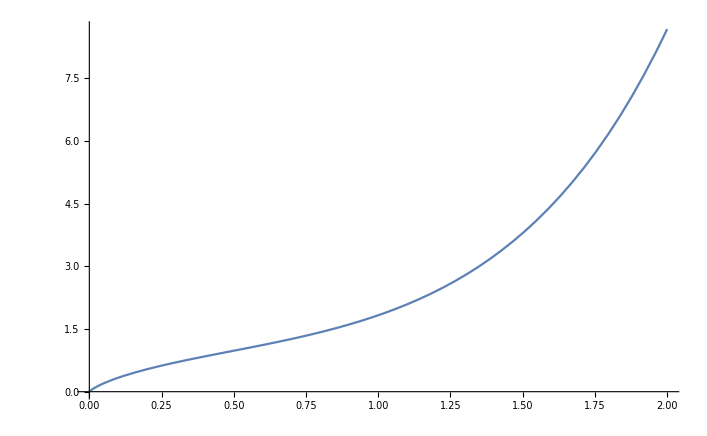

```mathematica
Plot[G[x],{x,0,2}]
```

Perfect Clock P(l1,l2<L1,L2)

```mathematica
Ln1=4;
Ln2=1;
```

```mathematica
Pc1[l1_,l2_,t_]:=Exp[-2*t]*t^(l1+l2)/(l1!l2!)
Pc2[l1_,L2_,t_]:=t^l1/(l1!)*Exp[-t]*(1-Exp[-t]*Sum[t^l2/(l2!),{l2,0,L2-1}])
```

```mathematica
Pc3[L1_,L2_,t_]:=1-Sum[Sum[Pc1[l1,l2,t],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[Pc2[l1,L2,t],{l1,0,L1-1}]-Sum[Pc2[l2,L1,t],{l2,0,L2-1}]
```

```mathematica
ENPC[L1_,L2_,t_]:=-(Sum[Sum[Pc1[l1,l2,t]*Log[Pc1[l1,l2,t]],{l1,0,L1-2}],{l2,0,L2-1}]+Sum[Pc2[l1,L2,t]*Log[Pc2[l1,L2,t]],{l1,0,L1-1}]+Sum[Pc2[l2,L1,t]*Log[Pc2[l2,L2,t]],{l2,0,L2-1}]+Pc3[L1,L2,t]*Log[Pc3[L1,L2,t]])
```

```mathematica
Plot[ENPC[4,1,t],{t,0,20}]
```

```mathematica
T1=Evaluate@Table[Pc1[l1,l2,t], {l1,0,Ln1-1},{l2,0,Ln2-1}]; 
T2=Evaluate@Table[Pc2[l1,Ln2,t],{l1,0,Ln1-1}];
T3=Evaluate@Table[Pc2[l1,Ln1,t],{l1,0,Ln2-1}];
T13=Evaluate@Table[t/.Solve[Pc1[l1,l2,t]==1/20&& t>0],{l1,0,Ln1-1},{l2,0,Ln2-1}];
T23=Evaluate@Table[τ/.Solve[Pc2[l1,Ln2,τ]==1/20&&τ>0],{l1,0,Ln1-1}];
T33=Evaluate@Table[τ/.Solve[Pc2[l1,Ln1,τ]==1/20&&τ>0],{l1,0,Ln2-1}];
L1=t/.Solve[Pc3[Ln1,Ln2,t]==1/20&&t>0];
```

```mathematica
a=0.2
```

```mathematica
L1
```

{Root[{-60-57 ⅇ^(2 #1)-60 #1-30 #1^2-10 #1^3+ⅇ^#1 (120+60 #1+30 #1^2+10 #1^3)&,1.4910730466715915063}]}

```mathematica
Root[{-60-57 ⅇ^(2 #1)-60 #1-30 #1^2-10 #1^3+ⅇ^#1 (120+60 #1+30 #1^2+10 #1^3)&,1.4910730466715915063479906651616016932289310337336498087404`20.602058556074585}]
```

Root[{-60-57 ⅇ^(2 #1)-60 #1-30 #1^2-10 #1^3+ⅇ^#1 (120+60 #1+30 #1^2+10 #1^3)&,1.4910730466715915063}]

```mathematica
N[Root[{-60-57 ⅇ^(2 #1)-60 #1-30 #1^2-10 #1^3+ⅇ^#1 (120+60 #1+30 #1^2+10 #1^3)&,1.4910730466715915063479906651616016932289310337336498087404`20.602058556074585}]]
```

1.49107

```mathematica
b1[x_]:=0.2/;x<T13[[1]][[1]]
b[x_]:=a*2/; T13[[2]][[1]][[1]]x<T13[[2]][[1]][[2]]
c[x_]:=a*3/;T13[[3]][[1]][[1]]<x<T13[[3]][[1]][[2]]
d[x_]:=a*4/;T23[[1]][[1]]<x<T23[[1]][[2]]
e[x_]:=a*5/;T23[[2]][[1]]<x<T23[[2]][[2]]
f[x_]:=a*6/;T23[[3]][[1]]<x<T23[[3]][[2]]
g[x_]:=a*7/;T23[[4]][[1]]<x<T23[[4]][[2]]
h[x_]:=a*8/;L1[[1]]<x
```

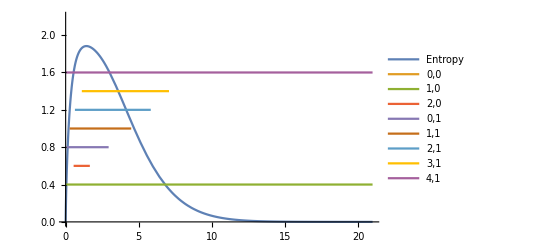

```mathematica
Plot[{ENPC[Ln1,Ln2,x],b1[x],b[x],c[x],d[x],e[x],f[x],g[x],h[x]},{x,0,21},PlotRange->{0,2.2},PlotLegends->{"Entropy","0,0","1,0","2,0","0,1","1,1","2,1","3,1","4,1"}]
```